## 1. LO & Optimize LO depth

The investor’s wealth process X_t is

ⅆ X_t=-(S_(t-)-δ_(t-))ⅆ N_t-(S_(t-)-Υ)ⅆ M_t^0

#### params

```mathematica
Δ=5*10^-3;0.005;
σ=0.01;
α=0.001;
ϕ=0.001;
γ=10;
κ=50;
ε=0.005;
Υ=Δ+ε;
χ=0.02;
tiltλ=50/300;
λ=N[50/300];

Ν=10;(*Total Amt*)
T=300;(*Total Time*)
```

```mathematica
(*Market Impact Cost*)
c[q_]:=α*q;
```

```mathematica
(*Target Schedule*)
IS[t_]:=Ν*(1-Sinh[χ*(T-t)]/Sinh[χ*T])
```

#### eqs

```mathematica
ω[t_,q_]:=ⅇ^(-κ*(Υ+c[Ν-q])*(Ν-q))/;t==T
ω[t_,q_]:=Exp[-κ*ϕ*NIntegrate[(Ν-IS[u])^2,{u,t,T}]]/;q==Ν
```

尝试解析解 建议告辞

```mathematica
eqs=(D[ω[t,q],t]-κ*ϕ*(q-IS[t])^2 ω[t,q]+ⅇ^-1 λ ω[t,q+1])*(ω[t,q]-ⅇ^(-κ*Υ)ω[t,q+1])==0
```

(ω[t,q]-0.606531 ω[t,1+q]) (-0.05 (q-10 (1-0.00495753 Sinh[0.02 (300-t)]))^2 ω[t,q]+0.0613132 ω[t,1+q]+ω^(1,0)[t,q])==0

数值解尝试
Do it backwards

```mathematica
fdmSolver[t_,nt_,q_]:=
Module[
{time=N@Subdivide[0,t,nt],
dt,
mat,
idxTrigger,
trigger
},
dt=First@Differences@time;
mat=ConstantArray[0,{q+1,Length[time]}];
mat[[-1]]=Table[ω[i,q],{i,time}];(*Q terminal condition*)
mat[[All,-1]]=Table[ω[t,i],{i,0,q}];(*T*)
trigger=ConstantArray[0,{q+1, Length[time]}];
(*trigger[[;;,-1]]=ConstantArray[1,q+1];*)
(*from t+dt to t*)
Do[
mat[[1;;-2,idxT]]=
mat[[1;;-2,idxT+1]]-
κ*ϕ*dt*
Thread[
Times[
Power[Range[0,q-1]-IS[time[[idxT+1]]],2],
mat[[1;;-2,idxT+1]]]]
+ⅇ^-1*λ*dt*mat[[2;;-1,idxT+1]];
idxTrigger=Boole[Thread[Less[mat[[1;;-2,idxT]], mat[[2;;-1,idxT]]*ⅇ^(-κ*Υ)]]];
AppendTo[idxTrigger,0];
trigger[[;;,idxT]]=idxTrigger;
mat[[1;;-2,idxT]]=MapThread[Max,{mat[[1;;-2,idxT]],ⅇ^(-κ*Υ)*mat[[2;;-1,idxT]]}];
,{idxT,Range[Length[time]-1,1,-1]}];
{mat,trigger}
]
```

```mathematica
{mat3,trigger} = fdmSolver[T,3000,10];
```

```mathematica
ListPlot3D@mat3
```

-Graphics3D-

```mathematica
findTrigger[triggerMat_,time_]:=
time[[DeleteCases[Table[
With[{row=triggerMat[[idxQ]]},
SelectFirst[
Range[Length@row],
row[[#]]==1&]],{idxQ,Length@triggerMat}],_Missing]]]
```

```mathematica
findTrigger2[triggerMat_,time_,l_]:=
time[[DeleteCases[Table[
With[{row=triggerMat[[idxQ]]},
SelectFirst[
Range[Length@row],
row[[#]]==l&]],{idxQ,Length@triggerMat}],_Missing]]]
```

```mathematica
Length@trigger
```

11

```mathematica
moSignals=findTrigger[trigger,N@Subdivide[0,T,3000] ]
```

{4.1,10.1,16.9,24.8,34.3,46.2,62.2,86.4,137.1,299.9}

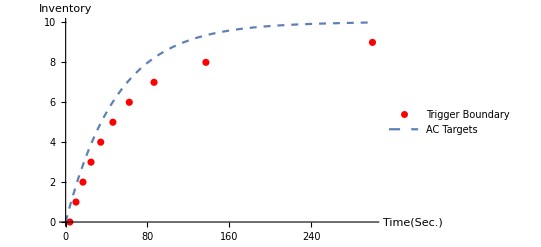

```mathematica
Show[
ListPlot[Transpose[{moSignals,Range[0,Length[moSignals]-1]}],PlotStyle->Red,PlotLegends->{"Trigger Boundary"}],
Plot[IS[i],{i,0,300},PlotStyle->Dashed,PlotLegends->{"AC Targets"}],
PlotRange->All,AxesLabel->{"Time(Sec.)","Inventory"}]
```

Find the optimal depth
δ(t,q) = 1/κ+h(t,q)-h(t,q+1)

```mathematica
optDepth[ω_]:=Module[{δ},
δ=ConstantArray[0,Dimensions[ω]];
Do[δ[[i]]=1/κ+1/κ*Log[ω[[i]]]-1/κ*Log[ω[[i+1]]],{i,1, Length[δ]-1}];
δ
]
```

```mathematica
optDepth[mat3]
```

{1}
 |  |  |  |

#### Price Dynamics

```mathematica
S0=100
```

100

```mathematica
𝒫=TransformedProcess[S0+σ*(up[t]-down[t]),{up\[Distributed]PoissonProcess[γ],down\[Distributed]PoissonProcess[γ]},t];
```

```mathematica
data = RandomFunction[𝒫,{0,T,.1},1]
```

TemporalData[…]

```mathematica
TWAP[price_]:=MovingMap[Mean,price,price["PathLength"],None]
```

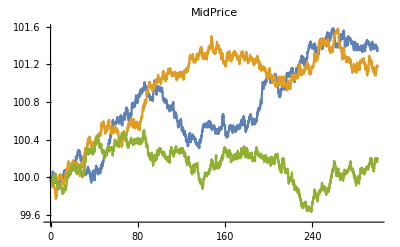
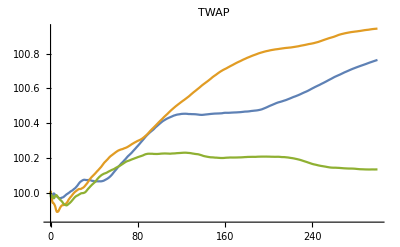

```mathematica
With[{data = RandomFunction[𝒫,{0,T,0.1},3]},
{ListLinePlot[data,PlotRange->All,PlotLabel->"MidPrice"], ListLinePlot[TWAP[data],PlotLabel->"TWAP"]}]
```

```mathematica
data = RandomFunction[𝒫,{0,T,.1},1];
moSignals;
loDepth=optDepth[mat3];
timeLine =N@Subdivide[0,T,3000];
dt=First@Differences@timeLine;
midPrice=Last@Transpose[First@Normal[data]];
```

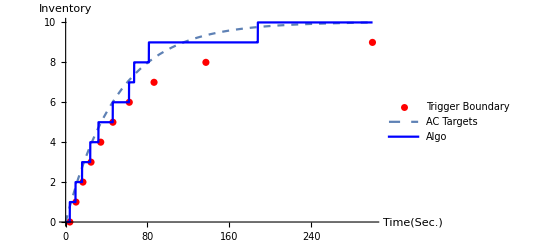

```mathematica
{inv,cash}=Module[
{inventory,
money,
curInv,
curTime,
depth,
isFilled,
isMO},
inventory=ConstantArray[0,3002];
money=ConstantArray[0,3002];
Do[
curInv=inventory[[i]];
curTime=timeLine[[i]];
(*If[inventory[[i]]== 10,Break[]];*)
depth=loDepth[[curInv+1]][[i]];
isFilled=RandomReal[1]<λ*ⅇ^(-κ*depth)*dt;
isMO=Ceiling[moSignals[[curInv+1]]]== Ceiling[curTime];
If[isFilled||isMO,inventory[[i]]+=1;money[[i]]+=midPrice[[i]]];
If[isFilled&& !isMO,money[[i]]-=depth ];
If[isMO && !isFilled,money[[i]]+=Υ];
inventory[[i+1]]=inventory[[i]];
money[[i+1]]=money[[i]];
If[inventory[[i]]== 10,inventory[[i;;-1]]=10;money[[i;;-1]]=money[[i]];Break[]];
,{i,1,3001}];
{Transpose[{timeLine,inventory[[;;-2]]}],money[[;;-2]]}];

Show[
ListPlot[Transpose[{moSignals,Range[0,Length[moSignals]-1]}],PlotStyle->Red,PlotLegends->{"Trigger Boundary"}],
Plot[IS[i],{i,0,300},PlotStyle->Dashed,PlotLegends->{"AC Targets"}],
ListLinePlot[inv,PlotStyle->Blue,PlotLegends->{"Algo"}],
PlotRange->All,AxesLabel->{"Time(Sec.)","Inventory"}]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

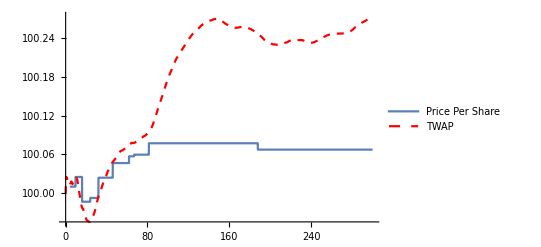

```mathematica
Show[ListLinePlot[DeleteCases[Transpose[{timeLine,cash/Last@Transpose@inv}],{_,Indeterminate}],PlotLegends->{"Price Per Share"}],ListLinePlot[TWAP[data],PlotStyle->{Dashed,Red},PlotLegends->{"TWAP"}],PlotRange-> All,AxesOrigin-> {0,Min[TWAP[data]]}]
```

```mathematica
AC=Table[IS[i],{i,timeLine}];
diff=Differences[AC];
amt=PrependTo[diff,First@AC];
money2=FoldList[Plus,amt*(midPrice+Υ)];
ACtwap=Transpose[{timeLine,money2/AC}]
```

{{0.,100.01},{0.1,100.03},{0.2,100.04},{0.3,100.04},{0.4,100.04},{0.5,100.04},{0.6,100.038},{0.7,100.037},{0.8,100.036},2983,{299.2,100.142},{299.3,100.142},{299.4,100.142},{299.5,100.142},{299.6,100.142},{299.7,100.142},{299.8,100.142},{299.9,100.142},{300.,100.142}}
 |  |  |  |

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

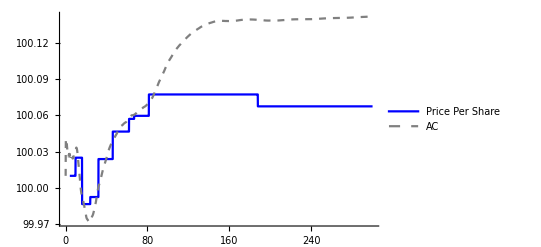

```mathematica
Show[ListLinePlot[DeleteCases[Transpose[{timeLine,cash/Last@Transpose@inv}],{_,Indeterminate}],PlotStyle->Blue,PlotLegends->{"Price Per Share"}],(*ListLinePlot[TWAP[data],PlotStyle->{Dashed,Red},PlotLegends->{"TWAP"}],*)
ListLinePlot[ACtwap,PlotStyle->{Dashed,Gray},PlotLegends->{"AC"}],
PlotRange-> All,AxesOrigin-> {0,99.9}]
```

## 2. Posting Only at the Touch

The trader submits only 1 LO at the best bid, otherwise MO.

```mathematica
(*Ternimal and Boundary Condition*)
```

```mathematica
h[t_/;t== T,q_]:=-(Υ+c[Ν-q])*(Ν-q)
```

```mathematica
h[t_,q_/; q==Ν]:=-ϕ*∫_t^T (Ν-IS[u])^2 ⅆu
```

```mathematica
ρ=N@(ⅇ^(-κ*Δ));
```

```mathematica
fdmSolverTouch[t_,nt_,q_]:=
Module[
{time=N@Subdivide[0,t,nt],
dt,
mat,
loTrigger,
moTrigger,
loIdx,
moIdx
},
(*time step increment*)
dt=First@Differences@time;
(*values*)
mat=ConstantArray[0,{q+1,Length[time]}];
(*behind boundary  signals for LO*)
loTrigger=ConstantArray[0,{q,Length[time]}];(*0 -> q-1*)
(*trigger boundary signals for MO*)
moTrigger=ConstantArray[0,{q,Length[time]}];(*0 -> q-1*)

(*Fill values of terminal & boundary condition *)
mat[[-1]]=Table[h[i,q],{i,time}];
mat[[All,-1]]=Table[h[t,i],{i,0,q}];

(*from t+dt to t, obtain values of h[t,q] from h[t+dt,q]*)
Do[
(*1;;-2 maps q= 0~N-1*)
mat[[1;;-2,idxT]]=
mat[[1;;-2,idxT+1]]+dt*ρ*λ*Ramp@(Δ+mat[[2;;-1,idxT+1]]-mat[[1;;-2,idxT+1]])-ϕ*dt*Power[Range[0,q-1]-IS[time[[idxT+1]]],2];

loIdx=Boole@Thread[Δ+mat[[2;;-1,idxT+1]]>mat[[1;;-2,idxT+1]]];
loTrigger[[;;,idxT]]=loIdx;

moIdx=Boole@Thread@(mat[[1;;-2,idxT]]< (mat[[2;;-1,idxT]]-Υ));
moTrigger[[;;,idxT]]=moIdx;

mat[[1;;-2,idxT]]=MapThread[Max,{mat[[1;;-2,idxT]],mat[[2;;-1,idxT]]-Υ}];,
{idxT,Range[Length[time]-1,1,-1]}];

{mat,loTrigger,moTrigger}
]
```

```mathematica
{mat1,lo1,mo1}=fdmSolverTouch[T,3000,Ν];
(*{mat2,lo2,mo2}=fdmSolverTouch[T,300,Ν];*)
```

```mathematica
ListPlot3D@mat1
```

-Graphics3D-

```mathematica
loSignals=findTrigger[lo1,timeLine];
```

```mathematica
loSignals
```

{0.,1.8,7.9,14.9,23.1,33.,45.4,62.1,87.6,142.5}

```mathematica
moSignals2=findTrigger[mo1,timeLine]
```

{5.2,11.4,18.4,26.6,36.5,48.9,65.6,90.9,144.9,299.9}

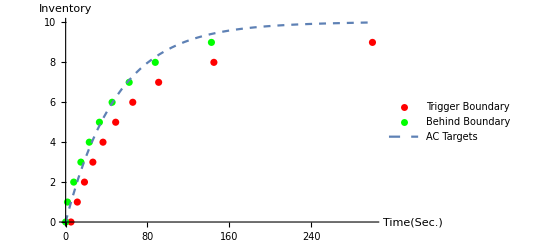

```mathematica
Show[
ListPlot[Transpose[{moSignals2,Range[0,Length[moSignals2]-1]}],PlotStyle->Red,PlotLegends->{"Trigger Boundary"}],
ListPlot[Transpose[{loSignals,Range[0,Length[loSignals]-1]}],PlotStyle->Green,PlotLegends->{"Behind Boundary"}],
Plot[IS[i],{i,0,300},PlotStyle->Dashed,PlotLegends->{"AC Targets"}],
PlotRange->All,AxesLabel->{"Time(Sec.)","Inventory"}]
```

## 5. Posting Only at the Touch and Optimizing Volume

The QVI for h is

max{∂_t h(t,q)+ρλMaximize[lΔ+h(t,q+l)-h(t,q),l]-(ϕ(q-q_t))^2; -Υ+h(t,q+1)-h(t,q)}=0

l ∈{0, 1, 2, ..., Ν-q}

l ≤ 2 here

```mathematica
fdmSolverTouchVolume[t_,nt_,q_]:=
Module[
{time=N@Subdivide[0,t,nt],
dt,
mat,
loTrigger,
moTrigger,
loIdx,
moIdx,
lstar,
maxValue
},
dt=First@Differences@time;
mat=ConstantArray[0,{q+1,Length[time]}];(*0 -> q*)
moTrigger=ConstantArray[0,{q,Length[time]}];(*0 -> q-1*)
loTrigger=ConstantArray[0,{q,Length[time]}];(*0 -> q-1*)
(* terminal & boundary condition *)
mat[[-1]]=Table[h[i,q],{i,time}];
mat[[All,-1]]=Table[h[t,i],{i,0,q}];

(*from t+dt to t*)
Do[
{lstar,maxValue}=Transpose@Table[
With[
{tb=Table[l*Δ+mat[[Evaluate@Min[i+l,q+1],idxT+1]]-mat[[i,idxT+1]],{l,{0,1,2}}]},
{Last@Flatten@Position[tb,Max[tb]]-1,Max[tb]}],{i,1,q}];
loTrigger[[;;,idxT+1]]=lstar;

mat[[1;;-2,idxT]]=
mat[[1;;-2,idxT+1]]+dt*ρ*λ*maxValue-ϕ*dt*Power[Range[0,q-1]-IS[time[[idxT+1]]],2];

moIdx=Boole@Thread@(mat[[1;;-2,idxT]]< (mat[[2;;-1,idxT]]-Υ));
moTrigger[[;;,idxT]]=moIdx;
mat[[1;;-2,idxT]]=MapThread[Max,{mat[[1;;-2,idxT]],mat[[2;;-1,idxT]]-Υ}];,
{idxT,Range[Length[time]-1,1,-1]}];
loTrigger[[;;,1]]=First@Transpose@Table[
With[
{tb=Table[l*Δ+mat[[Evaluate@Min[i+l,11],1]]-mat[[i,1]],{l,{0,1,2}}]},
{Last@Flatten@Position[tb,Max[tb]]-1,Max[tb]}],{i,1,q}];
{mat,loTrigger,moTrigger}
]
```

```mathematica
{mat2,lo2,mo2}=fdmSolverTouchVolume[T,3000,Ν];
```

```mathematica
loSignals21=findTrigger[lo2,timeLine]
```

{0.,2.3,8.3,15.3,23.4,33.2,45.6,62.3,87.7}

```mathematica
Length@loSignals21
```

9

```mathematica
Length@loSignals22
```

10

```mathematica
Length@moSignals3
```

10

```mathematica
moSignals3=findTrigger[mo2,timeLine]
```

{7.9,14.2,21.3,29.6,39.6,52.1,68.7,93.9,144.9,299.9}

```mathematica
loSignals22=findTrigger2[lo2,timeLine,2]
```

{2.3,8.3,15.3,23.4,33.2,45.6,62.3,87.7,194.,142.6}

```mathematica
Transpose[{loSignals21,Range[0,Ν-2]}]
```

{{0.,0},{2.3,1},{8.3,2},{15.3,3},{23.4,4},{33.2,5},{45.6,6},{62.3,7},{87.7,8}}

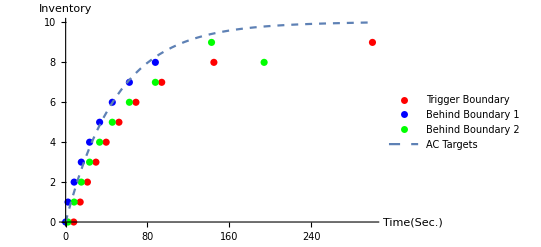

```mathematica
Show[
ListPlot[Transpose[{moSignals3,Range[0,(Length@moSignals3)-1]}],PlotStyle->Red,PlotLegends->{"Trigger Boundary"}],
ListPlot[Transpose[{loSignals21,Range[0,(Length@loSignals21)-1]}],PlotStyle->Blue,PlotLegends->{"Behind Boundary 1"}],
ListPlot[Transpose[{loSignals22,Range[0,Length@loSignals22-1]}],PlotStyle->Green,PlotLegends->{"Behind Boundary 2"}],
Plot[IS[i],{i,0,300},PlotStyle->Dashed,PlotLegends->{"AC Targets"}],
PlotRange->All,AxesLabel->{"Time(Sec.)","Inventory"}]
```

```mathematica
ListPlot3D@lo2
```

-Graphics3D-